# Thornburg 6 coordinate patches

## Notations

Global indices will be denoted by (i,j,k)

Local indices will be denoted by (a,b,c).

The triad that defines the global tensor basis is e_a^i.

The Jacobian of the transformation is J_ij=∂x^a/∂x^i.

## Global (Cartesian) to local transformations

Global coordinate system: Cartesian, i.e., (i,j,k)=(x,y,z).

Patches: 6 segments of the inflated square following Thornburg, i.e., (a,b,c)=(ρ,σ,r).

Patch parameters
r_0: Excision radius.
r_f: Outer radius.

```mathematica
thornburg6={
(*r0, rf*)
{2,10},

(* ± X patch *)
{Function[{x,z},ArcTan[z/x]],Function[{x,y},ArcTan[y/x]],Function[{x,y,z},√(x^2+y^2+z^2)]},

(* ± Y patch *)
{Function[{y,z},ArcTan[z/y]],Function[{x,y},ArcTan[x/y]],Function[{x,y,z},√(x^2+y^2+z^2)]},

(* ± Z patch *)
{Function[{y,z},ArcTan[y/z]],Function[{x,z},ArcTan[x/z]],Function[{x,y,z},√(x^2+y^2+z^2)]}
};

thornburg6Pure={
(*r0, rf*)
{2,10},

(* ± X patch *)
{ArcTan[z/x],ArcTan[y/x],√(x^2+y^2+z^2)},

(* ± Y patch *)
{ArcTan[z/y],ArcTan[x/y],√(x^2+y^2+z^2)},

(* ± Z patch *)
{ArcTan[y/z],ArcTan[x/z],√(x^2+y^2+z^2)}
};
```

## Jacobians

### +±X

```mathematica
JPMX=Table[D[thornburg6Pure⟦2,i⟧,{x,y,z}⟦j⟧],{i,1,3},{j,1,3}]//FullSimplify;
DJPMX=Table[D[JPMX⟦i,j⟧,{x,y,z}⟦k⟧],{i,1,3},{j,1,3},{k,1,3}]//FullSimplify;

MatrixForm[JPMX]
MatrixForm[DJPMX]
```

(-z/(x^2+z^2) | 0 | x/(x^2+z^2)
-y/(x^2+y^2) | x/(x^2+y^2) | 0
x/(√(x^2+y^2+z^2)) | y/(√(x^2+y^2+z^2)) | z/(√(x^2+y^2+z^2)))

(((2 x z)/((x^2+z^2)^2)
0
(-x^2+z^2)/((x^2+z^2)^2)) | (0
0
0) | ((-x^2+z^2)/((x^2+z^2)^2)
0
-(2 x z)/((x^2+z^2)^2))
((2 x y)/((x^2+y^2)^2)
(-x^2+y^2)/((x^2+y^2)^2)
0) | ((-x^2+y^2)/((x^2+y^2)^2)
-(2 x y)/((x^2+y^2)^2)
0) | (0
0
0)
((y^2+z^2)/((x^2+y^2+z^2)^(3/2))
-(x y)/((x^2+y^2+z^2)^(3/2))
-(x z)/((x^2+y^2+z^2)^(3/2))) | (-(x y)/((x^2+y^2+z^2)^(3/2))
(x^2+z^2)/((x^2+y^2+z^2)^(3/2))
-(y z)/((x^2+y^2+z^2)^(3/2))) | (-(x z)/((x^2+y^2+z^2)^(3/2))
-(y z)/((x^2+y^2+z^2)^(3/2))
(x^2+y^2)/((x^2+y^2+z^2)^(3/2))))

### +±Y

```mathematica
JPMY=Table[D[thornburg6Pure⟦3,i⟧,{x,y,z}⟦j⟧],{i,1,3},{j,1,3}]//FullSimplify;
DJPMY=Table[D[JPMY⟦i,j⟧,{x,y,z}⟦k⟧],{i,1,3},{j,1,3},{k,1,3}]//FullSimplify;

MatrixForm[JPMY]
MatrixForm[DJPMY]
```

(0 | -z/(y^2+z^2) | y/(y^2+z^2)
y/(x^2+y^2) | -x/(x^2+y^2) | 0
x/(√(x^2+y^2+z^2)) | y/(√(x^2+y^2+z^2)) | z/(√(x^2+y^2+z^2)))

((0
0
0) | (0
(2 y z)/((y^2+z^2)^2)
(-y^2+z^2)/((y^2+z^2)^2)) | (0
(-y^2+z^2)/((y^2+z^2)^2)
-(2 y z)/((y^2+z^2)^2))
(-(2 x y)/((x^2+y^2)^2)
((x-y) (x+y))/((x^2+y^2)^2)
0) | (((x-y) (x+y))/((x^2+y^2)^2)
(2 x y)/((x^2+y^2)^2)
0) | (0
0
0)
((y^2+z^2)/((x^2+y^2+z^2)^(3/2))
-(x y)/((x^2+y^2+z^2)^(3/2))
-(x z)/((x^2+y^2+z^2)^(3/2))) | (-(x y)/((x^2+y^2+z^2)^(3/2))
(x^2+z^2)/((x^2+y^2+z^2)^(3/2))
-(y z)/((x^2+y^2+z^2)^(3/2))) | (-(x z)/((x^2+y^2+z^2)^(3/2))
-(y z)/((x^2+y^2+z^2)^(3/2))
(x^2+y^2)/((x^2+y^2+z^2)^(3/2))))

### +±Z

```mathematica
JPMZ=Table[D[thornburg6Pure⟦4,i⟧,{x,y,z}⟦j⟧],{i,1,3},{j,1,3}]//FullSimplify;
DJPMZ=Table[D[JPMY⟦i,j⟧,{x,y,z}⟦k⟧],{i,1,3},{j,1,3},{k,1,3}]//FullSimplify;

MatrixForm[JPMZ]
MatrixForm[DJPMZ]
```

(0 | z/(y^2+z^2) | -y/(y^2+z^2)
z/(x^2+z^2) | 0 | -x/(x^2+z^2)
x/(√(x^2+y^2+z^2)) | y/(√(x^2+y^2+z^2)) | z/(√(x^2+y^2+z^2)))

((0
0
0) | (0
(2 y z)/((y^2+z^2)^2)
(-y^2+z^2)/((y^2+z^2)^2)) | (0
(-y^2+z^2)/((y^2+z^2)^2)
-(2 y z)/((y^2+z^2)^2))
(-(2 x y)/((x^2+y^2)^2)
((x-y) (x+y))/((x^2+y^2)^2)
0) | (((x-y) (x+y))/((x^2+y^2)^2)
(2 x y)/((x^2+y^2)^2)
0) | (0
0
0)
((y^2+z^2)/((x^2+y^2+z^2)^(3/2))
-(x y)/((x^2+y^2+z^2)^(3/2))
-(x z)/((x^2+y^2+z^2)^(3/2))) | (-(x y)/((x^2+y^2+z^2)^(3/2))
(x^2+z^2)/((x^2+y^2+z^2)^(3/2))
-(y z)/((x^2+y^2+z^2)^(3/2))) | (-(x z)/((x^2+y^2+z^2)^(3/2))
-(y z)/((x^2+y^2+z^2)^(3/2))
(x^2+y^2)/((x^2+y^2+z^2)^(3/2))))

## Visualization

### Visualizing the +X Part

```mathematica
thornburg6PlusXPlot=
Show[
(* r lines *)
ContourPlot[
thornburg6⟦2,3⟧[x,y,0],

{x,-10.5,10.5},
{y,-10.5,10.5},

ContourShading->None,
ContourStyle->Directive[Dashed,Green,Thick],

RegionFunction->Function[
{x,y,f},
x>0&&
-π/4≤thornburg6⟦2,2⟧[x,y]≤π/4
],

Contours->Range[thornburg6⟦1,1⟧,thornburg6⟦1,2⟧,(thornburg6⟦1,2⟧-thornburg6⟦1,1⟧)/9]⟦2;;-2⟧
],

(* σ lines *)
ContourPlot[
thornburg6⟦2,2⟧[x,y],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Dashed,Green,Thick],

RegionFunction->Function[
{x,y,f},
x>0&&
-π/4≤thornburg6⟦2,2⟧[x,y]≤π/4&&
thornburg6⟦1,1⟧≤thornburg6⟦2,3⟧[x,y,0]≤thornburg6⟦1,2⟧
],

Contours->Range[-π/4,π/4,π/(2*9)]⟦2;;-2⟧
],

(* r boundary *)
ContourPlot[
thornburg6⟦2,3⟧[x,y,0],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Red,Thick],

RegionFunction->Function[
{x,y,f},
x>0&&
-π/4≤thornburg6⟦2,2⟧[x,y]≤π/4
],

Contours->{thornburg6⟦1,1⟧,thornburg6⟦1,2⟧}
],

(* σ boundary *)
ContourPlot[
thornburg6⟦2,2⟧[x,y],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Red,Thick],

RegionFunction->Function[
{x,y,f},
x>0&&
-π/4≤thornburg6⟦2,2⟧[x,y]≤π/4&&
thornburg6⟦1,1⟧≤thornburg6⟦2,3⟧[x,y,0]≤thornburg6⟦1,2⟧
],

Contours->{-π/4,π/4}
]
];
```

### Visualizing the -X Part

```mathematica
thornburg6MinusXPlot=
Show[
(* r lines *)
ContourPlot[
thornburg6⟦2,3⟧[x,y,0],

{x,-10.5,10.5},
{y,-10.5,10.5},

ContourShading->None,
ContourStyle->Directive[Dashed,Green,Thick],

RegionFunction->Function[
{x,y,f},
x<0&&
-π/4≤thornburg6⟦2,2⟧[x,y]≤π/4
],

Contours->Range[thornburg6⟦1,1⟧,thornburg6⟦1,2⟧,(thornburg6⟦1,2⟧-thornburg6⟦1,1⟧)/9]⟦2;;-2⟧
],

(* σ lines *)
ContourPlot[
thornburg6⟦2,2⟧[x,y],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Dashed,Green,Thick],

RegionFunction->Function[
{x,y,f},
x<0&&
-π/4≤thornburg6⟦2,2⟧[x,y]≤π/4&&
thornburg6⟦1,1⟧≤thornburg6⟦2,3⟧[x,y,0]≤thornburg6⟦1,2⟧
],

Contours->Range[-π/4,π/4,π/(2*9)]⟦2;;-2⟧
],

(* r boundary *)
ContourPlot[
thornburg6⟦2,3⟧[x,y,0],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Red,Thick],

RegionFunction->Function[
{x,y,f},
x<0&&
-π/4≤thornburg6⟦2,2⟧[x,y]≤π/4
],

Contours->{thornburg6⟦1,1⟧,thornburg6⟦1,2⟧}
],

(* σ boundary *)
ContourPlot[
thornburg6⟦2,2⟧[x,y],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Red,Thick],

RegionFunction->Function[
{x,y,f},
x<0&&
-π/4≤thornburg6⟦2,2⟧[x,y]≤π/4&&
thornburg6⟦1,1⟧≤thornburg6⟦2,3⟧[x,y,0]≤thornburg6⟦1,2⟧
],

Contours->{-π/4,π/4}
]
];
```

### Visualizing the +Y Part

```mathematica
thornburg6PlusYPlot=
Show[
(* r lines *)
ContourPlot[
thornburg6⟦3,3⟧[x,y,0],

{x,-10.5,10.5},
{y,-10.5,10.5},

ContourShading->None,
ContourStyle->Directive[Dashed,Green,Thick],

RegionFunction->Function[
{x,y,f},
y>0&&
-π/4≤thornburg6⟦3,2⟧[x,y]≤π/4
],

Contours->Range[thornburg6⟦1,1⟧,thornburg6⟦1,2⟧,(thornburg6⟦1,2⟧-thornburg6⟦1,1⟧)/9]⟦2;;-2⟧
],

(* σ lines *)
ContourPlot[
thornburg6⟦3,2⟧[x,y],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Dashed,Green,Thick],

RegionFunction->Function[
{x,y,f},
y>0&&
-π/4≤thornburg6⟦3,2⟧[x,y]≤π/4&&
thornburg6⟦1,1⟧≤thornburg6⟦3,3⟧[x,y,0]≤thornburg6⟦1,2⟧
],

Contours->Range[-π/4,π/4,π/(2*9)]⟦2;;-2⟧
],

(* r boundary *)
ContourPlot[
thornburg6⟦3,3⟧[x,y,0],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Red,Thick],

RegionFunction->Function[
{x,y,f},
y>0&&
-π/4≤thornburg6⟦3,2⟧[x,y]≤π/4
],

Contours->{thornburg6⟦1,1⟧,thornburg6⟦1,2⟧}
],

(* σ boundary *)
ContourPlot[
thornburg6⟦3,2⟧[x,y],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Red,Thick],

RegionFunction->Function[
{x,y,f},
y>0&&
-π/4≤thornburg6⟦3,2⟧[x,y]≤π/4&&
thornburg6⟦1,1⟧≤thornburg6⟦3,3⟧[x,y,0]≤thornburg6⟦1,2⟧
],

Contours->{-π/4,π/4}
]
];
```

### Visualizing the -Y Part

```mathematica
thornburg6MinusYPlot=
Show[
(* r lines *)
ContourPlot[
thornburg6⟦3,3⟧[x,y,0],

{x,-10.5,10.5},
{y,-10.5,10.5},

ContourShading->None,
ContourStyle->Directive[Dashed,Green,Thick],

RegionFunction->Function[
{x,y,f},
y<0&&
-π/4≤thornburg6⟦3,2⟧[x,y]≤π/4
],

Contours->Range[thornburg6⟦1,1⟧,thornburg6⟦1,2⟧,(thornburg6⟦1,2⟧-thornburg6⟦1,1⟧)/9]⟦2;;-2⟧
],

(* σ lines *)
ContourPlot[
thornburg6⟦3,2⟧[x,y],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Dashed,Green,Thick],

RegionFunction->Function[
{x,y,f},
y<0&&
-π/4≤thornburg6⟦3,2⟧[x,y]≤π/4&&
thornburg6⟦1,1⟧≤thornburg6⟦3,3⟧[x,y,0]≤thornburg6⟦1,2⟧
],

Contours->Range[-π/4,π/4,π/(2*9)]⟦2;;-2⟧
],

(* r boundary *)
ContourPlot[
thornburg6⟦3,3⟧[x,y,0],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Red,Thick],

RegionFunction->Function[
{x,y,f},
y<0&&
-π/4≤thornburg6⟦3,2⟧[x,y]≤π/4
],

Contours->{thornburg6⟦1,1⟧,thornburg6⟦1,2⟧}
],

(* σ boundary *)
ContourPlot[
thornburg6⟦3,2⟧[x,y],

{x,-10,10},
{y,-10,10},

ContourShading->None,
ContourStyle->Directive[Red,Thick],

RegionFunction->Function[
{x,y,f},
y<0&&
-π/4≤thornburg6⟦3,2⟧[x,y]≤π/4&&
thornburg6⟦1,1⟧≤thornburg6⟦3,3⟧[x,y,0]≤thornburg6⟦1,2⟧
],

Contours->{-π/4,π/4}
]
];
```

### Visualizing the XY plane of the patch

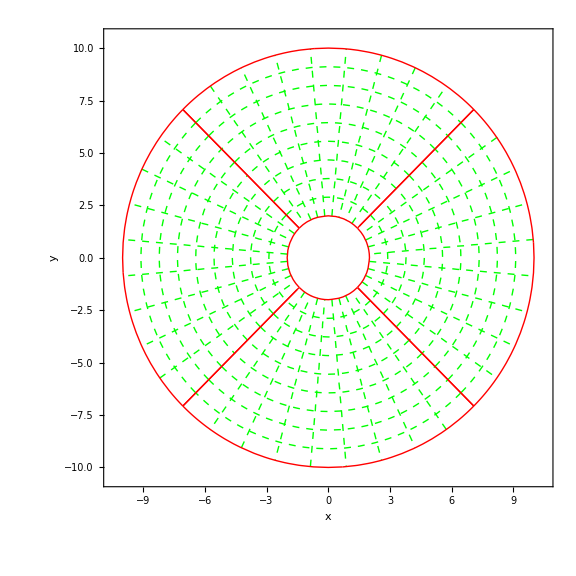

```mathematica
Show[
thornburg6PlusXPlot,
thornburg6MinusXPlot,
thornburg6PlusYPlot,
thornburg6MinusYPlot,
ImageSize->Large,
FrameLabel->{"x","y"}
]
```